Definicje funkcji używanych przy mapowaniu:

```mathematica
GetMax[x_] :={First[x], Max[Take[x,{2,Length[x]}]]};
```

```mathematica
GetMean[x_] :={First[x], Mean[Take[x,{2,Length[x]}]]};
```

```mathematica
GetVariance[x_] :={First[x], Variance[Take[x,{2,Length[x]}]]};
```

```mathematica
GetPlusStandardDeviation[x_] :={First[x],Mean[Take[x,{2,Length[x]}]] + StandardDeviation[Take[x,{2,Length[x]}]]};
```

```mathematica
GetMinusStandardDeviation[x_] :={First[x],Mean[Take[x,{2,Length[x]}]] - StandardDeviation[Take[x,{2,Length[x]}]]};
```

Pobieranie danych i mapowanie ich do funkcji:

```mathematica
insertRaw := ReadList["/home/dev/Workspaces/Studies/AnalAlgo/PriorityQueue/queue_insert.m", Number, RecordLists->True];
insertMax:=Map[GetMax, insertRaw];
insertMean:=Map[GetMean, insertRaw];
insertVariance:=Map[GetVariance, insertRaw];
insertPlusStandardDeviation := Map[GetPlusStandardDeviation, insertRaw];
insertMinusStandardDeviation := Map[GetMinusStandardDeviation, insertRaw];
```

```mathematica
findMinRaw := ReadList["/home/dev/Workspaces/Studies/AnalAlgo/PriorityQueue/queue_find_min.m", Number, RecordLists->True];
findMinMax:=Map[GetMax, findMinRaw];
findMinMean:=Map[GetMean, findMinRaw];
findMinVariance:=Map[GetVariance, findMinRaw];
findMinPlusStandardDeviation := Map[GetPlusStandardDeviation, findMinRaw];
findMinMinusStandardDeviation := Map[GetMinusStandardDeviation, findMinRaw];
```

```mathematica
extractMinRaw := ReadList["/home/dev/Workspaces/Studies/AnalAlgo/PriorityQueue/queue_extract_min.m", Number, RecordLists->True];
extractMinMax:=Map[GetMax, extractMinRaw];
extractMinMean:=Map[GetMean, extractMinRaw];
extractMinVariance:=Map[GetVariance, extractMinRaw];
extractMinPlusStandardDeviation := Map[GetPlusStandardDeviation, extractMinRaw];
extractMinMinusStandardDeviation := Map[GetMinusStandardDeviation, extractMinRaw];
```

```mathematica
decreaseKeyRaw := ReadList["/home/dev/Workspaces/Studies/AnalAlgo/PriorityQueue/queue_decrease_key.m", Number, RecordLists->True];
decreaseKeyMax:=Map[GetMax, decreaseKeyRaw];
decreaseKeyMean:=Map[GetMean, decreaseKeyRaw];
decreaseKeyVariance:=Map[GetVariance, decreaseKeyRaw];
decreaseKeyPlusStandardDeviation := Map[GetPlusStandardDeviation, decreaseKeyRaw];
decreaseKeyMinusStandardDeviation := Map[GetMinusStandardDeviation, decreaseKeyRaw];
```

```mathematica
deleteRaw := ReadList["/home/dev/Workspaces/Studies/AnalAlgo/PriorityQueue/queue_delete.m", Number, RecordLists->True];
deleteMax:=Map[GetMax, deleteRaw];
deleteMean:=Map[GetMean, deleteRaw];
deleteVariance:=Map[GetVariance, deleteRaw];
deletePlusStandardDeviation := Map[GetPlusStandardDeviation, deleteRaw];
deleteMinusStandardDeviation := Map[GetMinusStandardDeviation, deleteRaw];
```

```mathematica
unionRaw := ReadList["/home/dev/Workspaces/Studies/AnalAlgo/PriorityQueue/queue_delete.m", Number, RecordLists->True];
unionMax:=Map[GetMax, unionRaw];
unionMean:=Map[GetMean, unionRaw];
unionVariance:=Map[GetVariance, unionRaw];
unionPlusStandardDeviation := Map[GetPlusStandardDeviation, unionRaw];
unionMinusStandardDeviation := Map[GetMinusStandardDeviation, unionRaw];
```

Wyświetlanie wyników dla operacji insert:

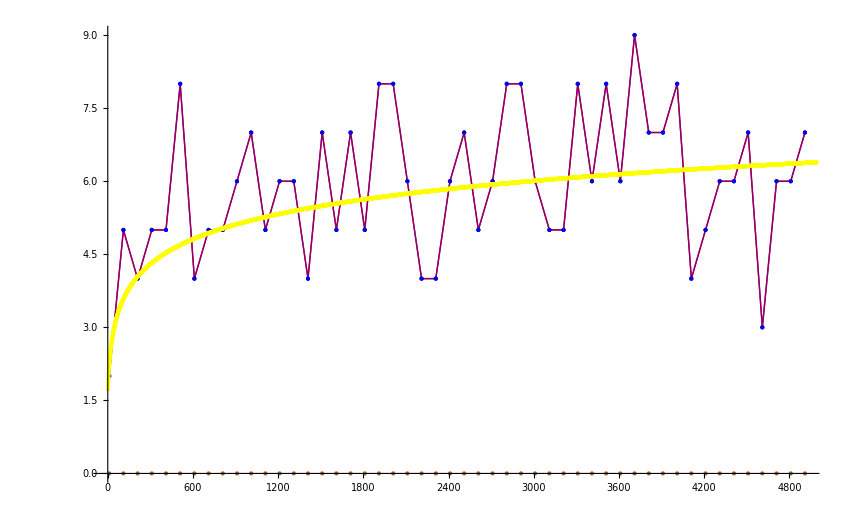

```mathematica
Show[
ListLinePlot[insertPlusStandardDeviation,PlotStyle->Red],
ListLinePlot[insertMinusStandardDeviation,PlotStyle->Purple],
ListPlot[insertMax,PlotStyle -> Black],
ListPlot[insertMean,PlotStyle -> Blue],
ListPlot[insertVariance, PlotStyle->Brown],
ListPlot[Table[0.75Log[n],{n, 10, 5000}], PlotStyle-> Yellow]
]
```

Wyświetlanie wyników dla operacji find min:

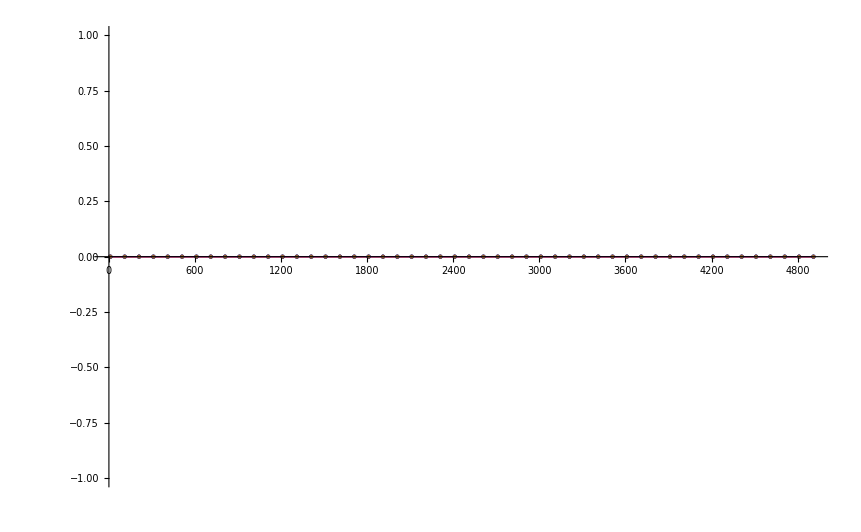

```mathematica
Show[
ListLinePlot[findMinPlusStandardDeviation,PlotStyle->Red],
ListLinePlot[findMinMinusStandardDeviation,PlotStyle->Purple],
ListPlot[findMinMax,PlotStyle -> Black],
ListPlot[findMinMean,PlotStyle -> Blue],
ListPlot[findMinVariance, PlotStyle->Brown]
]
```

Wyświetlanie wyników dla operacji extract min:

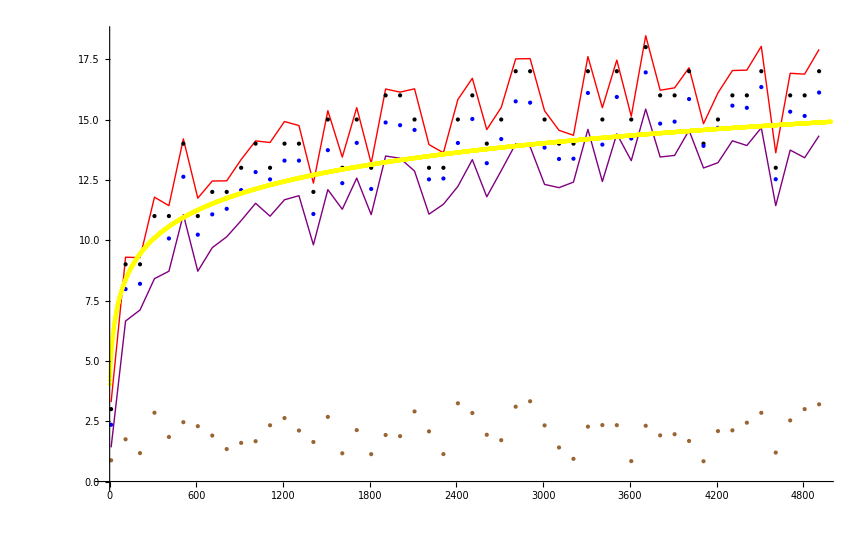

```mathematica
Show[
ListLinePlot[extractMinPlusStandardDeviation,PlotStyle->Red],
ListLinePlot[extractMinMinusStandardDeviation,PlotStyle->Purple],
ListPlot[extractMinMax,PlotStyle -> Black],
ListPlot[extractMinMean,PlotStyle -> Blue],
ListPlot[extractMinVariance, PlotStyle->Brown],
ListPlot[Table[1.75Log[n],{n, 10, 5000}], PlotStyle-> Yellow]
]
```

Wyświetlanie wyników dla operacji decrease key:

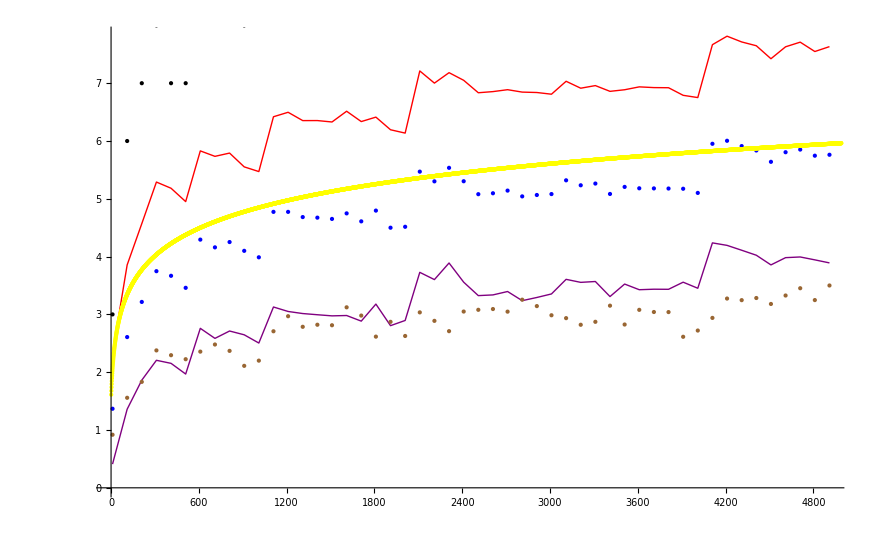

```mathematica
Show[
ListLinePlot[decreaseKeyPlusStandardDeviation,PlotStyle->Red],
ListLinePlot[decreaseKeyMinusStandardDeviation,PlotStyle->Purple],
ListPlot[decreaseKeyMax,PlotStyle -> Black],
ListPlot[decreaseKeyMean,PlotStyle -> Blue],
ListPlot[decreaseKeyVariance, PlotStyle->Brown],
ListPlot[Table[0.7Log[n],{n, 10, 5000}], PlotStyle-> Yellow]
]
```

Wyświetlanie wyników dla operacji delete:

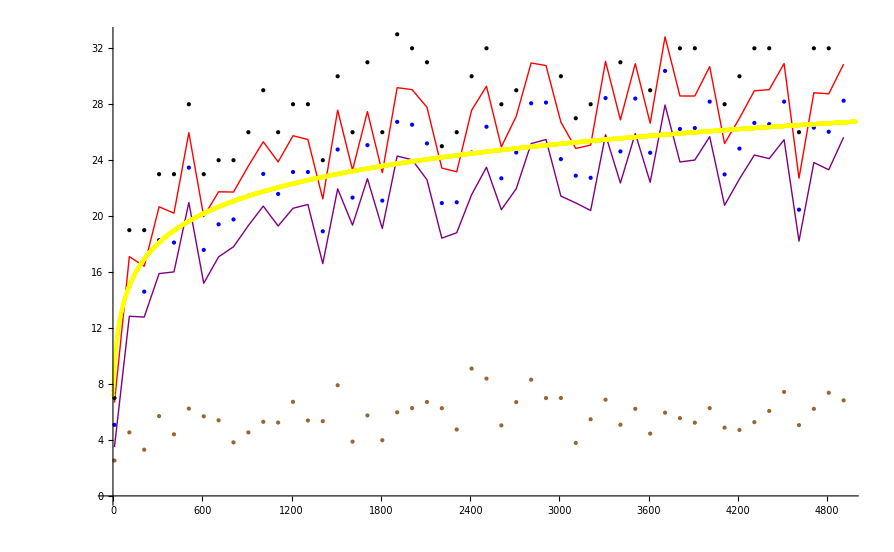

```mathematica
Show[
ListLinePlot[deletePlusStandardDeviation,PlotStyle->Red],
ListLinePlot[deleteMinusStandardDeviation,PlotStyle->Purple],
ListPlot[deleteMax,PlotStyle -> Black],
ListPlot[deleteMean,PlotStyle -> Blue],
ListPlot[deleteVariance, PlotStyle->Brown],
ListPlot[Table[Pi Log[n],{n, 10, 5000}], PlotStyle-> Yellow]
]
```

Wyświetlanie wyników dla operacji union:

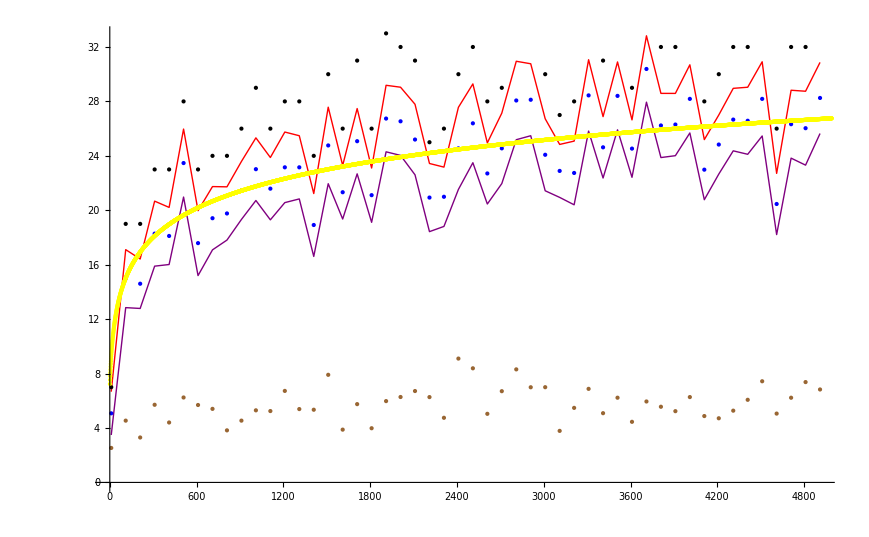

```mathematica
Show[
ListLinePlot[unionPlusStandardDeviation,PlotStyle->Red],
ListLinePlot[unionMinusStandardDeviation,PlotStyle->Purple],
ListPlot[unionMax,PlotStyle -> Black],
ListPlot[unionMean,PlotStyle -> Blue],
ListPlot[unionVariance, PlotStyle->Brown],
ListPlot[Table[Pi Log[n],{n, 10, 5000}], PlotStyle-> Yellow]
]
```